```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\e0013233\Dropbox\module\mathematica\prismpair

```mathematica
degtorad[θ_]:=θ*π/180
radtodeg[θ_]:=θ*180/π

(*define rotation matrix with rotation axis coindcide with x-axis*)
rotx[ϕ_]:={{1,0,0},{0,Cos[ϕ],-Sin[ϕ]},{0,Sin[ϕ],Cos[ϕ]}}

(*A function to draw prism, we make the center of the prism flat surface at (0,0)*)
prism[θ_,ϕ_,x_,sign_]:={rotx[ϕ].{sign 4Tan[degtorad[θ]]+x,-2,2},rotx[ϕ].{0+x,-2,2},rotx[ϕ].{0+x,-2,-2},rotx[ϕ].{sign 4Tan[degtorad[θ]]+x,2,2},rotx[ϕ].{0+x,2,2},rotx[ϕ].{0+x,2,-2}}

(*Snell's law in 3D,
n1,n2 are refractive index of medium 1 and 2,
l is normalised incoming beam vector,
n is normalised plane normal vector
*)
vrefrac[n1_,n2_,l_,n_]:=n1/n2 l+(-n1/n2 (n.l)-√(1-(n1/n2)^2(1-(n.l)^2)))n

(*parameter to get the intersection point of beam and surface of prism,
lo a point in the incoming beam,
vecline is the normalised vector of the beam,
po is a point on a plane,
nsurf is normalised plane normal vector*)
intpara[lo_,vecline_,po_,nsurf_]:=((po-lo).nsurf)/(vecline.nsurf)

(*Surface vector of a surface*)
survec[θ_,ϕ_,sign_]:=rotx[ϕ].{sign Cos[θ],0,-Sin[θ]}

(*Arctan for 2π domain*)
atan2new[x_,y_]:=If[x==0&& y<0,3π/2,If[x==0&& y>0,π/2,
If[x>0&& y≥0,ArcTan[Abs[y/x]],
If[x<0&& y>0,π-ArcTan[Abs[y/x]],
If[x<0&& y≤ 0,π+ArcTan[Abs[y/x]],
If[x>0&& y<0,2π-ArcTan[Abs[y/x]]]
]]]]]
```

```mathematica
Manipulate[Show[
{Graphics3D[{Orange,Thick,
(*The line show the normal vector of first surface*)
Line[{{-2Tan[degtorad[θ1]]+x1,0,0},{-2Tan[degtorad[θ1]]+x1,0,0}+2survec[degtorad[θ1],degtorad[ϕ1],-1]}],
(*Draw first prism*)
Green,Opacity[.3],Prism[prism[θ1,degtorad[ϕ1],x1,-1]],
(*The line show the normal vector of first surface*)
Orange,Thick,Line[{{2Tan[degtorad[θ2]]+x2,0,0},{2Tan[degtorad[θ2]]+x2,0,0}+2survec[degtorad[θ2],degtorad[ϕ2],1]}],
(*Draw second prism*)
Blue,Opacity[.3],Prism[prism[θ2,degtorad[ϕ2],x2,1]],

Red,Thick,Line[{{-5,5 Tan[degtorad[α]],5 Tan[degtorad[β]]},
{-2Tan[degtorad[θ1]]+x1,0,0},
{-2Tan[degtorad[θ1]]+x1,0,0}+
intpara[{-2Tan[degtorad[θ1]]+x1,0,0},
vrefrac[1,n1,Normalize[{-2Tan[degtorad[θ1]]+x1,0,0}-{-5,5 Tan[degtorad[α]],5 Tan[degtorad[β]]}],
survec[degtorad[θ1],degtorad[ϕ1],-1]],
{2Tan[degtorad[θ2]]+x2,0,0},
survec[degtorad[θ2],degtorad[ϕ2],1]] 

vrefrac[1,n1,Normalize[{-2Tan[degtorad[θ1]]+x1,0,0}-{-5,5 Tan[degtorad[α]],5 Tan[degtorad[β]]}],survec[degtorad[θ1],degtorad[ϕ1],-1]],
{-2Tan[degtorad[θ1]]+x1,0,0}+
intpara[{-2Tan[degtorad[θ1]]+x1,0,0},
vrefrac[1,n1,Normalize[{-2Tan[degtorad[θ1]]+x1,0,0}-{-5,5 Tan[degtorad[α]],5 Tan[degtorad[β]]}],
survec[degtorad[θ1],degtorad[ϕ1],-1]],
{2Tan[degtorad[θ2]]+x2,0,0},
survec[degtorad[θ2],degtorad[ϕ2],1]] 
vrefrac[1,n1,Normalize[{-2Tan[degtorad[θ1]]+x1,0,0}-{-5,5 Tan[degtorad[α]],5 Tan[degtorad[β]]}],survec[degtorad[θ1],degtorad[ϕ1],-1]]+
50vrefrac[n2,1,vrefrac[1,n1,Normalize[{-2Tan[degtorad[θ1]]+x1,0,0}-{-5,5 Tan[degtorad[α]],5 Tan[degtorad[β]]}],survec[degtorad[θ1],degtorad[ϕ1],-1]],-survec[degtorad[θ2],degtorad[ϕ2],1]]
}]

},PlotRange->{{-5,5},{-5,5},{-5,5}},Axes->True]}],{θ1,5,45},{{ϕ1,0},-180,180},{θ2,5,45},{{ϕ2,0},-180,180},{{x1,0},-2,0},{{x2,0},0,2},{{n1,1.5},1,2},{{n2,1.5},1,2},{{α,0},-90,90},{{β,0},-90,90}]
```

```mathematica
(*The trajectory of beam when both prism rotate in opposite direction*)
```

```mathematica
Manipulate[Show[{Graphics3D[{Orange,Thick,Line[{{-2Tan[degtorad[θ1]]+x1,0,0},{-2Tan[degtorad[θ1]]+x1,0,0}+2survec[degtorad[θ1],degtorad[ϕ1],-1]}],Green,Opacity[.3],Prism[prism[θ1,degtorad[ϕ1],x1,-1]],
Orange,Thick,Line[{{2Tan[degtorad[θ2]]+x2,0,0},{2Tan[degtorad[θ2]]+x2,0,0}+2survec[degtorad[θ2],degtorad[-ϕ1],1]}],
Blue,Opacity[.3],Prism[prism[θ2,degtorad[-ϕ1],x2,1]],
Black,Line[{{5,0,5},{5,0,-5}}],
Red,Thick,Line[{{-5,5 Tan[degtorad[α]],5 Tan[degtorad[β]]},
{-2Tan[degtorad[θ1]]+x1,0,0},
{-2Tan[degtorad[θ1]]+x1,0,0}+
intpara[{-2Tan[degtorad[θ1]]+x1,0,0},
vrefrac[1,n1,Normalize[{-2Tan[degtorad[θ1]]+x1,0,0}-{-5,5 Tan[degtorad[α]],5 Tan[degtorad[β]]}],
survec[degtorad[θ1],degtorad[ϕ1],-1]],
{2Tan[degtorad[θ2]]+x2,0,0},
survec[degtorad[θ2],degtorad[-ϕ1],1]] 

vrefrac[1,n1,Normalize[{-2Tan[degtorad[θ1]]+x1,0,0}-{-5,5 Tan[degtorad[α]],5 Tan[degtorad[β]]}],survec[degtorad[θ1],degtorad[ϕ1],-1]],
{-2Tan[degtorad[θ1]]+x1,0,0}+
intpara[{-2Tan[degtorad[θ1]]+x1,0,0},
vrefrac[1,n1,Normalize[{-2Tan[degtorad[θ1]]+x1,0,0}-{-5,5 Tan[degtorad[α]],5 Tan[degtorad[β]]}],
survec[degtorad[θ1],degtorad[ϕ1],-1]],
{2Tan[degtorad[θ2]]+x2,0,0},
survec[degtorad[θ2],degtorad[-ϕ1],1]] 
vrefrac[1,n1,Normalize[{-2Tan[degtorad[θ1]]+x1,0,0}-{-5,5 Tan[degtorad[α]],5 Tan[degtorad[β]]}],survec[degtorad[θ1],degtorad[ϕ1],-1]]+
50vrefrac[n2,1,vrefrac[1,n1,Normalize[{-2Tan[degtorad[θ1]]+x1,0,0}-{-5,5 Tan[degtorad[α]],5 Tan[degtorad[β]]}],survec[degtorad[θ1],degtorad[ϕ1],-1]],-survec[degtorad[θ2],degtorad[-ϕ1],1]]
}]

},PlotRange->{{0,5},{-5,5},{-5,5}},Axes->True]}],{θ1,5,45},{{ϕ1,0},-180,180},{θ2,5,45},{{x1,0},-2,0},{{x2,0},0,2},{{n1,1.5},1,2},{{n2,1.5},1,2},{{α,0},-90,90},{{β,0},-90,90}]
```

```mathematica
(*The trajectory of beam when both prism rotate in same direction*)
Manipulate[Show[{Graphics3D[{Orange,Thick,Line[{{-2Tan[degtorad[θ1]]+x1,0,0},{-2Tan[degtorad[θ1]]+x1,0,0}+2survec[degtorad[θ1],degtorad[ϕ1],-1]}],Green,Opacity[.3],Prism[prism[θ1,degtorad[ϕ1],x1,-1]],
Orange,Thick,Line[{{2Tan[degtorad[θ2]]+x2,0,0},{2Tan[degtorad[θ2]]+x2,0,0}+2survec[degtorad[θ2],degtorad[ϕ1],1]}],
Blue,Opacity[.3],Prism[prism[θ2,degtorad[ϕ1],x2,1]],
Black,Line[{{5,0,5},{5,0,-5}}],
Red,Thick,Line[{{-5,5 Tan[degtorad[α]],5 Tan[degtorad[β]]},
{-2Tan[degtorad[θ1]]+x1,0,0},
{-2Tan[degtorad[θ1]]+x1,0,0}+
intpara[{-2Tan[degtorad[θ1]]+x1,0,0},
vrefrac[1,n1,Normalize[{-2Tan[degtorad[θ1]]+x1,0,0}-{-5,5 Tan[degtorad[α]],5 Tan[degtorad[β]]}],
survec[degtorad[θ1],degtorad[ϕ1],-1]],
{2Tan[degtorad[θ2]]+x2,0,0},
survec[degtorad[θ2],degtorad[-ϕ1],1]] 

vrefrac[1,n1,Normalize[{-2Tan[degtorad[θ1]]+x1,0,0}-{-5,5 Tan[degtorad[α]],5 Tan[degtorad[β]]}],survec[degtorad[θ1],degtorad[ϕ1],-1]],
{-2Tan[degtorad[θ1]]+x1,0,0}+
intpara[{-2Tan[degtorad[θ1]]+x1,0,0},
vrefrac[1,n1,Normalize[{-2Tan[degtorad[θ1]]+x1,0,0}-{-5,5 Tan[degtorad[α]],5 Tan[degtorad[β]]}],
survec[degtorad[θ1],degtorad[ϕ1],-1]],
{2Tan[degtorad[θ2]]+x2,0,0},
survec[degtorad[θ2],degtorad[ϕ1],1]] 
vrefrac[1,n1,Normalize[{-2Tan[degtorad[θ1]]+x1,0,0}-{-5,5 Tan[degtorad[α]],5 Tan[degtorad[β]]}],survec[degtorad[θ1],degtorad[ϕ1],-1]]+
50vrefrac[n2,1,vrefrac[1,n1,Normalize[{-2Tan[degtorad[θ1]]+x1,0,0}-{-5,5 Tan[degtorad[α]],5 Tan[degtorad[β]]}],survec[degtorad[θ1],degtorad[ϕ1],-1]],-survec[degtorad[θ2],degtorad[ϕ1],1]]
}]

},PlotRange->{{0,5},{-2,2},{-2,2}},Axes->True]}],{θ1,5,45},{{ϕ1,0},-180,180},{θ2,5,45},{{x1,0},-2,0},{{x2,0},0,2},{{n1,1.5},1,2},{{n2,1.5},1,2},{{α,0},-90,90},{{β,0},-90,90}]
```

```mathematica
(*Scan through second prism when fixing the rotation angle of first prism*)
```

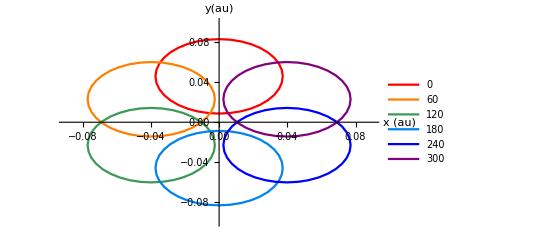

rings.EPS

```mathematica
planedot=Table[Drop[
Normalize[{-2Tan[degtorad[5]],0,0}+intpara[{-2Tan[degtorad[5]],0,0},
vrefrac[1,1.5,Normalize[{-2Tan[degtorad[5]],0,0}-{-5,5 Tan[degtorad[0]],5 Tan[degtorad[0]]}],
survec[degtorad[5],degtorad[ϕ1],-1]],
{2Tan[degtorad[5]],0,0},
survec[degtorad[5],degtorad[ϕ2],1]] 
vrefrac[1,1.5,Normalize[{-2Tan[degtorad[5]],0,0}-{-5,5 Tan[degtorad[0]],5 Tan[degtorad[0]]}],survec[degtorad[5],degtorad[ϕ1],-1]]+
vrefrac[1.5,1,vrefrac[1,1.5,Normalize[{-2Tan[degtorad[5]],0,0}-{-5,5 Tan[degtorad[0]],5 Tan[degtorad[0]]}],survec[degtorad[5],degtorad[ϕ1],-1]],-survec[degtorad[5],degtorad[ϕ2],1]]],1],{ϕ1,0,360,60},{ϕ2,0,360,10}];
colour={Red,Orange,ColorData[1,"ColorList"][[4]],ColorData[3,"ColorList"][[6]],Blue,Purple};
ringplot=Show[ListPlot[planedot[[1]],PlotRange->{{-.09,.09},{-0.1,0.1}},Joined->True,PlotStyle->colour[[1]],PlotLegends->LineLegend[colour,{0,60,120,180,240,300},LegendFunction->"Frame"],AxesLabel->{"x (au)","y(au)"}],Table[ListPlot[planedot[[i]],PlotRange->{{-.09,.09},{-0.1,0.13}},Joined->True,PlotStyle->colour[[i]]],{i,2,Length[planedot]-1}]]
Export["rings.EPS",ringplot]
```

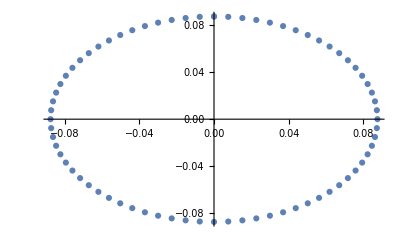

```mathematica
(*The trajectory of beam when both prism rotate in same direction*)
planedot2=Table[Drop[Normalize[{-2Tan[degtorad[5]],0,0}+intpara[{-2Tan[degtorad[5]],0,0},
vrefrac[1,1.5,Normalize[{-2Tan[degtorad[5]],0,0}-{-5,5 Tan[degtorad[0]],5 Tan[degtorad[0]]}],
survec[degtorad[5],degtorad[ϕ1],-1]],
{2Tan[degtorad[5]],0,0},
survec[degtorad[5],degtorad[ϕ1],1]] vrefrac[1,1.5,Normalize[{-2Tan[degtorad[5]],0,0}-{-5,5 Tan[degtorad[0]],5 Tan[degtorad[0]]}],survec[degtorad[5],degtorad[ϕ1],-1]]+
50vrefrac[1.5,1,vrefrac[1,1.5,Normalize[{-2Tan[degtorad[5]],0,0}-{-5,5 Tan[degtorad[0]],5 Tan[degtorad[0]]}],survec[degtorad[5],degtorad[ϕ1],-1]],-survec[degtorad[5],degtorad[ϕ1],1]]],1],{ϕ1,0,360,5}];
ListPlot[planedot2]
```

```mathematica
(*The trajectory of beam when both prism rotate in opposite direction*)
```

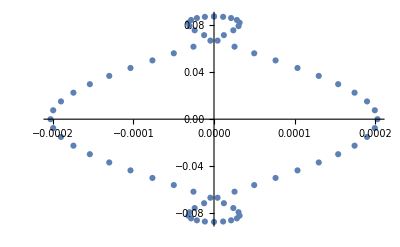

```mathematica
planedot4=Table[Drop[Normalize[{-2Tan[degtorad[5]],0,0}+intpara[{-2Tan[degtorad[5]],0,0},
vrefrac[1,1.5,Normalize[{-2Tan[degtorad[5]],0,0}-{-5,5 Tan[degtorad[0]],5 Tan[degtorad[0]]}],
survec[degtorad[5],degtorad[ϕ1],-1]],
{2Tan[degtorad[5]],0,0},
survec[degtorad[5],degtorad[-ϕ1],1]] vrefrac[1,1.5,Normalize[{-2Tan[degtorad[5]],0,0}-{-5,5 Tan[degtorad[0]],5 Tan[degtorad[0]]}],survec[degtorad[5],degtorad[ϕ1],-1]]+
50vrefrac[1.5,1,vrefrac[1,1.5,Normalize[{-2Tan[degtorad[5]],0,0}-{-5,5 Tan[degtorad[0]],5 Tan[degtorad[0]]}],survec[degtorad[5],degtorad[ϕ1],-1]],-survec[degtorad[5],degtorad[-ϕ1],1]]],1],{ϕ1,0,360,5}];
ListPlot[planedot4]
```

```mathematica
(*The trajectory of beam when both prism rotate in opposite direction express in polar and azimuth angle*)
```

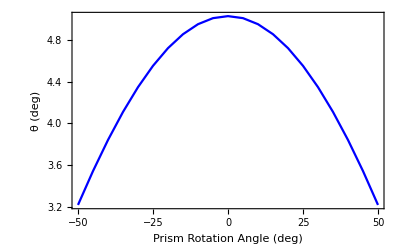
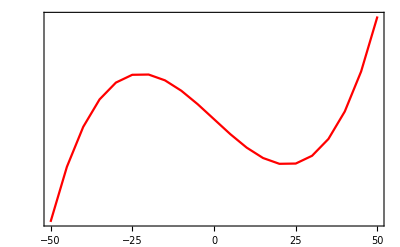

polarplot.EPS

```mathematica
planedot3=Table[Normalize[{-2Tan[degtorad[5]],0,0}+intpara[{-2Tan[degtorad[5]],0,0},
vrefrac[1,1.5,Normalize[{-2Tan[degtorad[5]],0,0}-{-5,5 Tan[degtorad[0]],5 Tan[degtorad[0]]}],
survec[degtorad[5],degtorad[ϕ1],-1]],
{2Tan[degtorad[5]],0,0},
survec[degtorad[5],degtorad[-ϕ1],1]] vrefrac[1,1.5,Normalize[{-2Tan[degtorad[5]],0,0}-{-5,5 Tan[degtorad[0]],5 Tan[degtorad[0]]}],survec[degtorad[5],degtorad[ϕ1],-1]]+
50vrefrac[1.5,1,vrefrac[1,1.5,Normalize[{-2Tan[degtorad[5]],0,0}-{-5,5 Tan[degtorad[0]],5 Tan[degtorad[0]]}],survec[degtorad[5],degtorad[ϕ1],-1]],-survec[degtorad[5],degtorad[-ϕ1],1]]],{ϕ1,-50,50,5}];
(*The azimuth angle, which is the arctan of y / z*)
azimuthangle=Table[{5 i-55, radtodeg[atan2new[planedot3[[i,2]],planedot3[[i,3]]]]-90},{i,1,Length[planedot3]}];
(*The polar angle, which is the arcCos of x*)
polarangle=Table[{5 i-55, radtodeg[ArcCos[planedot3[[i,1]]]]},{i,1,Length[planedot3]}];
plot2=ListPlot[azimuthangle,ImagePadding->45,Frame->{True,False,False,True},FrameLabel->{{None,"ϕ (deg)"},{None,None}},Axes->False
,FrameStyle->{Automatic,Automatic,Automatic,Red},FrameTicks->{{None,All},{All,None}},PlotStyle->Red,Joined->True];
plot1=ListPlot[polarangle,PlotStyle->Blue,ImagePadding->45,Frame->{True,True,True,False},FrameLabel->{{"θ (deg)",None},{"Prism Rotation Angle (deg)",None}},FrameStyle->{Automatic,Blue,Automatic,Automatic},Joined->True];
polarplot=Overlay[{plot1,plot2}]
Export["polarplot.EPS",polarplot]
```